```mathematica
vertices={{1,0,5000},{2,1000,5000},{3,3500,5000},{4,4500,5000},{5,5000,5000},{6,1000,4000},{7,2000,4000},{8,3500,4000},{9,0,3500},{10,1000,3500},{11,2000,3000},{12,3500,3000},{13,4500,3000},{14,1000,2000},{15,2000,2000},{16,3500,2000},{17,4500,2000},{18,5000,2000},{19,0,1500},{20,1000,1500},{21,3500,1000},{22,4000,1000},{23,5000,1000},{24,0,500},{25,1000,500},{26,3500,500},{27,0,0},{28,3500,0},{29,4000,0},{30,5000,0}};
```

```mathematica
aristas={{1,2,1000},{2,6,1000},{6,10,500},{9,10,1000},{1,9,1500},{2,3,2500},{3,8,1000},{7,8,1500},{6,7,1000},{3,4,1000},{4,13,2000},{12,13,1000},{8,12,1000},{4,5,500},{5,18,3000},{17,18,500},{13,17,1000},{7,11,1000},{11,15,1000},{14,15,1000},{10,14,1500},{11,12,1500},{14,20,500},{19,20,1000},{9,19,2000},{16,17,1000},{15,16,1500},{16,21,1000},{21,26,500},{25,26,2500},{20,25,1000},{18,23,1000},{22,23,1000},{21,22,500},{24,25,1000},{19,24,1000},{22,29,1000},{28,29,500},{26,28,500},{23,30,1000},{29,30,1000},{27,28,3500},{24,27,500}};
```

{{0,5000},{1000,5000},{1000,4000},{1000,3500},{0,3500},{3500,5000},{3500,4000},{2000,4000},{4500,5000},{4500,3000},{3500,3000},{5000,5000},{5000,2000},{4500,2000},{2000,3000},{2000,2000},{1000,2000},{1000,1500},{0,1500},{3500,2000},{3500,1000},{3500,500},{1000,500},{5000,1000},{4000,1000},{0,500},{4000,0},{3500,0},{5000,0},{0,0}}

{1<->2,2<->6,6<->10,9<->10,1<->9,2<->3,3<->8,7<->8,6<->7,3<->4,4<->13,12<->13,8<->12,4<->5,5<->18,17<->18,13<->17,7<->11,11<->15,14<->15,10<->14,11<->12,14<->20,19<->20,9<->19,16<->17,15<->16,16<->21,21<->26,25<->26,20<->25,18<->23,22<->23,21<->22,24<->25,19<->24,22<->29,28<->29,26<->28,23<->30,29<->30,27<->28,24<->27}

{1000,1000,500,1000,1500,2500,1000,1500,1000,1000,2000,1000,1000,500,3000,500,1000,1000,1000,1000,1500,1500,500,1000,2000,1000,1500,1000,500,2500,1000,1000,1000,500,1000,1000,1000,500,500,1000,1000,3500,500}

{{0,5000},{1000,5000},{1000,4000},{1000,3500},{0,3500},{3500,5000},{3500,4000},{2000,4000},{4500,5000},{4500,3000},{3500,3000},{5000,5000},{5000,2000},{4500,2000},{2000,3000},{2000,2000},{1000,2000},{1000,1500},{0,1500},{3500,2000},{3500,1000},{3500,500},{1000,500},{5000,1000},{4000,1000},{0,500},{4000,0},{3500,0},{5000,0},{0,0}}

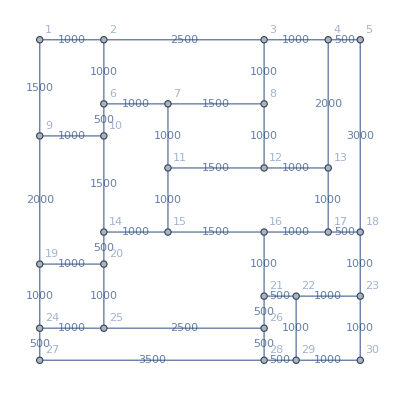

```mathematica
origen={1,2,3,4,5,9,18,19,23,24,27,28,29,30};

banderas = {{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0}};

conexiones={};
pesos = {};
coordenadas={};

For[x=1,x≤Length[aristas],x++,
AppendTo[pesos,aristas[[x]][[3]] ];
AppendTo[conexiones,aristas[[x]][[1]]<->aristas[[x]][[2]] ];
]


For[x=1,x≤Length[aristas],x++,
aux = aristas[[x]][[1]];
i =Position[banderas,aux][[1]][[1]];

If[  banderas[[i]][[2]]==0,
banderas[[i]][[2]]=1;
j = Position[vertices,aux][[1]][[1]];
AppendTo[coordenadas,{vertices[[j]][[2]],vertices[[j]][[3]]  }]
];

aux = aristas[[x]][[2]];
i =Position[banderas,aux][[1]][[1]];
If[  banderas[[i]][[2]]==0,
banderas[[i]][[2]]=1;
j = Position[vertices,aux][[1]][[1]];
AppendTo[coordenadas,{vertices[[j]][[2]],vertices[[j]][[3]]  }]
]
]

coordenadas

(*
vertices[[1]][[3]]

aux = aristas[[1]][[1]]
If[  banderas[[1]][[2]]==0,
banderas[[1]][[2]]=1;
j = Position[vertices,aux][[1]][[1]];
Print[j];
AppendTo[coordenadas,{vertices[[j]][[2]],vertices[[j]][[3]]}]
]

*)
conexiones
pesos
coordenadas
eEdges=Map[conexiones_⟦#⟧->pesos_⟦#⟧&,Range[Length[pesos]]];
grafo =Graph[conexiones,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->pesos,VertexCoordinates->coordenadas,EdgeLabels->eEdges];

grafo
```